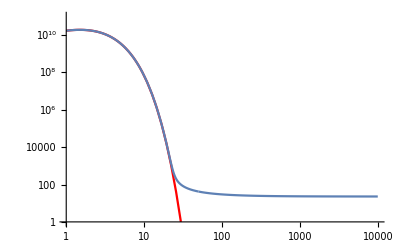

```mathematica
m=1000;
g=100;
σ=10^-10;
M=2.44 10^18;
solution1=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,50}];
bc=Evaluate[y[50]/.solution1];
solution2=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[50]==bc},
y,{x,50,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,50},PlotRange->{{1,10000},{1,10^11}}];
LogLogPlot[Evaluate[y[x]/.solution2],{x,50,10000},PlotRange->{{1,10000},{1,10^11}}];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},PlotStyle->RGBColor[1,0,0]];
Show[%,%%,%%%]
```

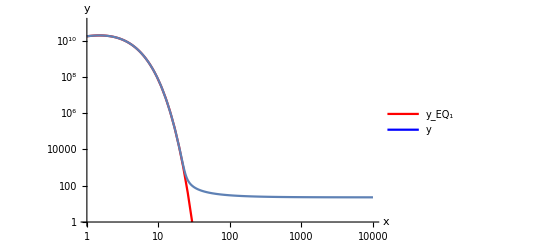

```mathematica
m=1000;
g=100;
σ=10^-10;
M=2.44 10^18;
solution1=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,10}];
bc=Evaluate[y[10]/.solution1];
solution2=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[10]==bc},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]},PlotLegends->  LineLegend[{Red,Blue},{"y_EQ_1","y"}]];
LogLogPlot[Evaluate[y[x]/.solution2],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
Show[%,%%,%%%]
```

{6.72584×10^7}

{6.72588×10^6}

{672626.}

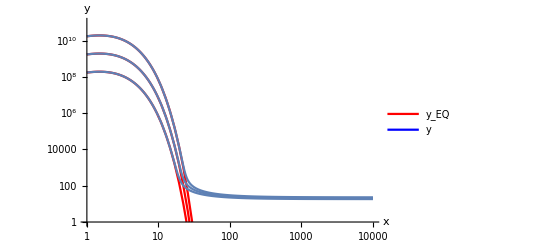

```mathematica
m=1000;
g=100;
M=2.44 10^18;


σ=10^-10;
solution1=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,10}];
bc=Evaluate[y[10]/.solution1];
solution2=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[10]==bc},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]},PlotLegends->  LineLegend[{Red,Blue},{"y_EQ","y"}]];
LogLogPlot[Evaluate[y[x]/.solution2],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p1=Show[%,%%,%%%];

σ1=10^-11;
solution11=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ1* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ1 *1^(3/2) E^-1},
y,{x,1,10}];
bc1=Evaluate[y[10]/.solution11];
solution21=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ1* x^(3/2) E^-x)^2),y[10]==bc1},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution21],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ1 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p2=Show[%,%%,%%%];

σ11=10^-12;
solution111=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ11* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ11 *1^(3/2) E^-1},
y,{x,1,10}];
bc11=Evaluate[y[10]/.solution111];
solution211=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[10]==bc11},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution211],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ11 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p3=Show[%,%%,%%%];

Show[p1,p2,p3]
```

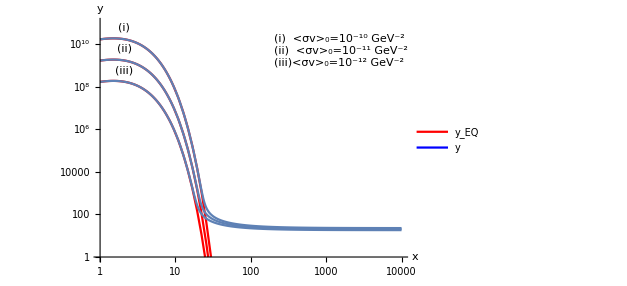

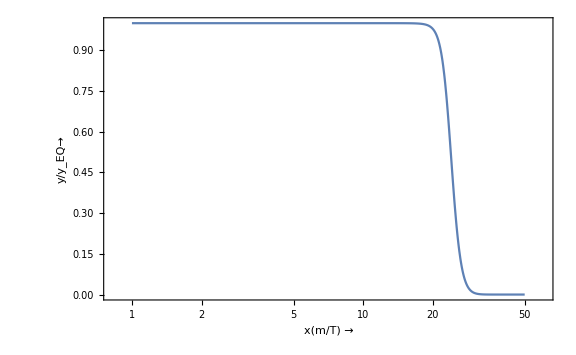

```mathematica
m=1000;
g=100;
σ=10^-10;
M=2.44 10^18;
solution1=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,50}];
LogLinearPlot[0.192 *M* m *σ* x^(3/2) E^-x/ Evaluate [y[x] /. solution1[[1]]],{x,1,50},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x(m/T) →","y/y_EQ→"},LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
m=1000;
g=100;
M=2.44 10^18;


σ=10^-10;
mm==1000GeV;
solution1=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,10}];
bc=Evaluate[y[10]/.solution1]
solution2=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[10]==bc},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]},PlotLegends->  LineLegend[{Red,Blue},{"y_EQ","y"}]];
LogLogPlot[Evaluate[y[x]/.solution2],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p1=Show[%,%%,%%%];

σ1=10^-12;
mm1==100000GeV;
solution11=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ1* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ1 *1^(3/2) E^-1},
y,{x,1,10}];
bc1=Evaluate[y[10]/.solution11]
solution21=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ1* x^(3/2) E^-x)^2),y[10]==bc1},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution21],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ1 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p2=Show[%,%%,%%%];

σ11=10^-9;
mm2==100GeV;
solution111=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ11* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ11 *1^(3/2) E^-1},
y,{x,4.0000001,4.0000002}, MaxStepSize->0.001];
bc11=Evaluate[y[4.0000002]/.solution111]
solution211=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[4.0000002]==bc11},
y,{x,4.0000002,40}];
bc111=Evaluate[y[40]/.solution211]
solution2111=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[40]==bc111},
y,{x,40,10000}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,4.0000001,4.0000002},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution211],{x,4.0000002,40},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution2111],{x,40,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ11 *x^(3/2) E^-x,{x,4.0000002,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p3=Show[%,%%,%%%];

Show[p1,p2,p3]
```

{6.72584×10^7}

{672626.}

{6.86441×10^10}

{{67.5695}}

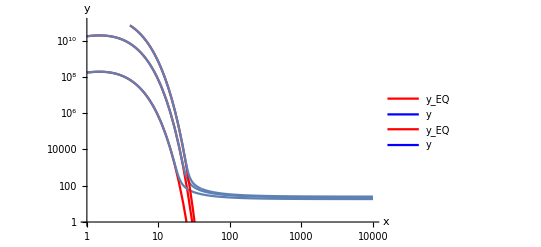

```mathematica
m=1000;
g=100;
M=2.44 10^18;


σ=10^-10;
solution1=NDSolve[{y'[x]==-(1/x^3) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,10}];
bc=Evaluate[y[10]/.solution1];
solution2=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[10]==bc},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]},PlotLegends->  LineLegend[{Red,Blue},{"y_EQ","y"}]];
LogLogPlot[Evaluate[y[x]/.solution2],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p1=Show[%,%%,%%%];

σ1=10^-11;
solution11=NDSolve[{y'[x]==-(1/x^3) (y[x]^2-(0.192 *M* m *σ1* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ1 *1^(3/2) E^-1},
y,{x,1,10}];
bc1=Evaluate[y[10]/.solution11];
solution21=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ1* x^(3/2) E^-x)^2),y[10]==bc1},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution21],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ1 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p2=Show[%,%%,%%%];

σ11=10^-12;
solution111=NDSolve[{y'[x]==-(1/x^3) (y[x]^2-(0.192 *M* m *σ11* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ11 *1^(3/2) E^-1},
y,{x,1,10}];
bc11=Evaluate[y[10]/.solution111];
solution211=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[10]==bc11},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution211],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ11 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p3=Show[%,%%,%%%];

Show[p1,p2,p3]
```

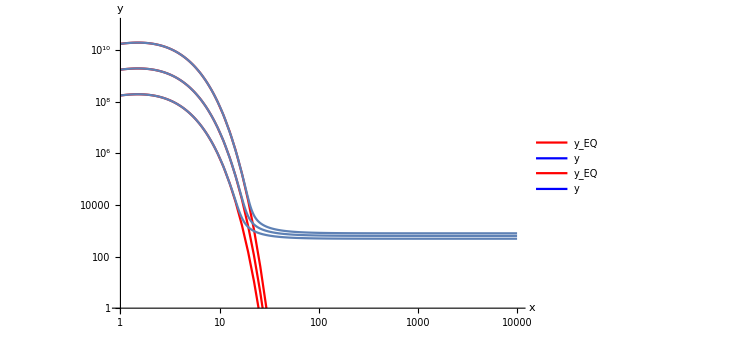

{6.72588×10^7}

{673008.}

{6.86441×10^10}

{{1397.59}}

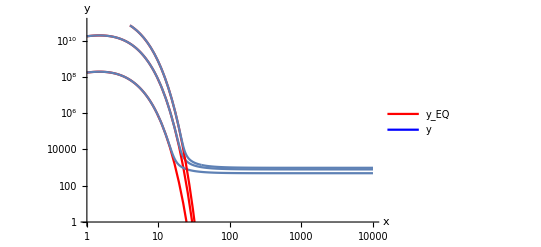

```mathematica
m=1000;
g=100;
M=2.44 10^18;


σ=10^-10;
mm==1000GeV;
solution1=NDSolve[{y'[x]==-(1/x^3) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,10}];
bc=Evaluate[y[10]/.solution1]
solution2=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[10]==bc},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]},PlotLegends->  LineLegend[{Red,Blue},{"y_EQ","y"}]];
LogLogPlot[Evaluate[y[x]/.solution2],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p1=Show[%,%%,%%%];

σ1=10^-12;
mm1==100000GeV;
solution11=NDSolve[{y'[x]==-(1/x^3) (y[x]^2-(0.192 *M* m *σ1* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ1 *1^(3/2) E^-1},
y,{x,1,10}];
bc1=Evaluate[y[10]/.solution11]
solution21=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ1* x^(3/2) E^-x)^2),y[10]==bc1},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution21],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ1 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p2=Show[%,%%,%%%];

σ11=10^-9;
mm2==100GeV;
solution111=NDSolve[{y'[x]==-(1/x^3) (y[x]^2-(0.192 *M* m *σ11* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ11 *1^(3/2) E^-1},
y,{x,4.0000001,4.0000002}, MaxStepSize->0.001];
bc11=Evaluate[y[4.0000002]/.solution111]
solution211=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[4.0000002]==bc11},
y,{x,4.0000002,40}];
bc111=Evaluate[y[40]/.solution211]
solution2111=NDSolve[{y'[x]==-(1/x^3)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[40]==bc111},
y,{x,40,10000}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,4.0000001,4.0000002},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution211],{x,4.0000002,40},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[Evaluate[y[x]/.solution2111],{x,40,10000},PlotRange->{{1,10000},{1,10^11}},AxesLabel-> {Style[x,Medium,Black],Style[y,Medium,Black]}];
LogLogPlot[0.192 *M *m * σ11 *x^(3/2) E^-x,{x,4.0000002,1000},PlotRange->{{1,10000},{1,10^11}},AxesLabel->{Style[x,Medium, Black],Style[y,Medium,Black]},PlotStyle->RGBColor[1,0,0]];
p3=Show[%,%%,%%%];

Show[p1,p2,p3]
```

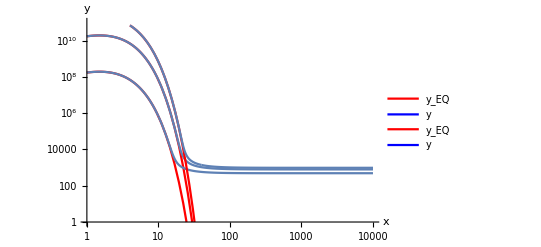

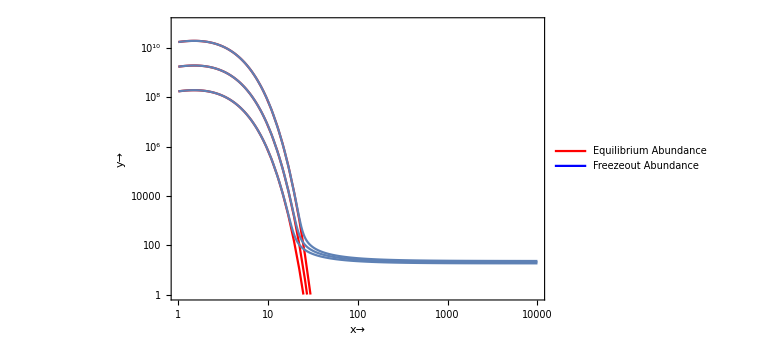

```mathematica
m=1000;
g=100;
M=2.44 10^18;


σ=10^-10;
solution1=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ *1^(3/2) E^-1},
y,{x,1,10}];
bc=Evaluate[y[10]/.solution1];
solution2=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ* x^(3/2) E^-x)^2),y[10]==bc},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution1],{x,1,10},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], ImageSize->Large];
LogLogPlot[Evaluate[y[x]/.solution2],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], ImageSize->Large];
LogLogPlot[0.192 *M *m * σ *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], ImageSize->Large,PlotStyle->RGBColor[1,0,0],LabelStyle->{Bold}];
p1=Show[%,%%,%%%];

σ1=10^-11;
solution11=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ1* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ1 *1^(3/2) E^-1},
y,{x,1,10}];
bc1=Evaluate[y[10]/.solution11];
solution21=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ1* x^(3/2) E^-x)^2),y[10]==bc1},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution11],{x,1,10},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], ImageSize->Large];
LogLogPlot[Evaluate[y[x]/.solution21],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], ImageSize->Large];
LogLogPlot[0.192 *M *m * σ1 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], LabelStyle->{Bold},ImageSize->Large,PlotStyle->RGBColor[1,0,0]];
p2=Show[%,%%,%%%];

σ11=10^-12;
solution111=NDSolve[{y'[x]==-(1/x^2) (y[x]^2-(0.192 *M* m *σ11* x^(3/2) E^-x)^2),
y[1]==0.192*M*m *σ11 *1^(3/2) E^-1},
y,{x,1,10}];
bc11=Evaluate[y[10]/.solution111];
solution211=NDSolve[{y'[x]==-(1/x^2)(y[x]^2-(0.192 *M* m* σ11* x^(3/2) E^-x)^2),y[10]==bc11},
y,{x,10,10000}];
LogLogPlot[Evaluate[y[x]/.solution111],{x,1,10},PlotRange->{{1,10000},{1,10^11}},PlotLegends->  LineLegend[{Red,Blue},{"Equilibrium Abundance","Freezeout Abundance"}], Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,15], ImageSize->Large];
LogLogPlot[Evaluate[y[x]/.solution211],{x,10,10000},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,Bold,12],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium], ImageSize->Large];
LogLogPlot[0.192 *M *m * σ11 *x^(3/2) E^-x,{x,1,1000},PlotRange->{{1,10000},{1,10^11}},Frame-> True,FrameTicksStyle->Directive[Black,Bold,15],FrameLabel->{"x→","y→"},LabelStyle->Directive[Black,Bold, Medium,20], ImageSize->Large,PlotStyle->RGBColor[1,0,0]];
p3=Show[%,%%,%%%];

Show[p1,p2,p3]
```